```mathematica
​
​
Remove["Global`*"];
wallyBrew2[printing_]:=Module[{},
T=600;(* closing time UNITS IN MINUTES *)
t=0;(* current time *)
ta=0;(* time of the next arrival *)
td1=∞;(* departure time of the current customer being served in section1 *)
td2=∞;(* departure time of the current customer being served *)
Na=0;(* total number of arrivals up to the current time *)

Nd1=0;(* total number of departures up to the current time at section 1*)
Nd2=0;(* total number of departures up to the current time at section 2 *)
Nl1=0;(* total number of lost customers at section 1*)
Nl2=0;(* total number of lost customers at section 2*)
Atimes1={};(* list of arrival times, per customer  at section 1*)
Dtimes1={};(* list of departure times, per customer at section 2 *)
Wtimes1={};(* list of waiting times, per customer at section 1 *)
Atimes2={};(* list of arrival times, per customer  at section 2*)
Dtimes2={};(* list of departure times, per customer at section 2 *)
Wtimes2={};(* list of waiting times, per customer at section 2*)
n1=0;(* number of customers in the system at the current time at section 1 *)
n2=0;(* number of customers in the system at the current time at section 2*)

(* list of the system state value, n, during simulation *) 
nlist1 = {n1}; 
nlist2 = {n2};
printTable={{"Event Type","Time","Na","Nd1","Nd2","n1","n2","ta","td1","td2"}};
U:=Random[];
λa[t_]:=Which[0≤t<120,1/6+t/240,120≤t<240,2/3,240≤t<600,1-t/720];
X:=-(1/λa[t]) Log[U];
Z:=Sqrt[-2 Log[U]]*Cos[2 π U];
Ya:=0.5 Z+1.5;(*Service time at section 1 station A*)
Yb:=0.5 Z+0.5;(*Service time at section 1 station B*)
Yc:=0.5 Z+0.5;(*Service time at section 1 station C*)
ta=X;(* set the first event as an arrival *)
stop=0;(* control variable for the iteration *)
(* turn on or off print statements throughout the code ... 
input parameter printing=1 will display tabular output *)
While[stop==0,If[ta<=Min[td1,td2]&&ta<=T,t=ta;
Na+=1;(*Handle arrival events*)
(*Update time and total arrivals*)
If[U<0.7,If[n1<5,n1+=1;(*70% chance to go to section 1*)
AppendTo[Atimes1,t];
If[n1==1,td1=t+Ya+Yb];(*set departure time if first in line*)
AppendTo[printTable,{"Arrival Section 1",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];,Nl1+=1;(*Increment lost customers if the line is longer than 5*)
AppendTo[printTable,{"Lost Section 1",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];],If[n2<5,n2+=1;(*Same logic for section 2*)
AppendTo[Atimes2,t];
If[n2==1,td2=t+Yc];
AppendTo[printTable,{"Arrival Section 2",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];,Nl2+=1;
AppendTo[printTable,{"Lost Section 2",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];]];
ta=t+X;,If[td1<=Min[ta,td2]&&td1<=T,t=td1;
n1-=1;
Nd1+=1;
AppendTo[Dtimes1,t];
If[n1>0,td1=t+Ya+Yb,td1=∞];
AppendTo[printTable,{"Departure Section 1",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];,If[td2<ta&&td2<=T,t=td2;
n2-=1;
Nd2+=1;
AppendTo[Dtimes2,t];
If[n2>0,td2=t+Yc,td2=∞];
AppendTo[printTable,{"Departure Section 2",t,Na,Nd1,Nd2,n1,n2,ta,td1,td2}];,(*end simulation if past closing time and all customer have 
;eft*)If[ta>T&&td1>T&&td2>T,Tp=Max[t-T,0];
stop=1;]]]];
AppendTo[nlist1,n1];
AppendTo[nlist2,n2];];
(*helper function to safely compute mean of a list,handling empty lists*)
safeMean[list_]:=Which[Length[list]==0,0,Length[list]==1,First[list],True,Mean[list]];
(*comput waiting times for each section*)
calculateWaitingTimes[arrivalTimes_,departureTimes_]:=Module[{lenArrival,lenDeparture,waitTimes},lenArrival=Length[arrivalTimes];
lenDeparture=Length[departureTimes];
If[lenArrival==lenDeparture,waitTimes=departureTimes-arrivalTimes,waitTimes={};];
waitTimes];
Wtimes1=calculateWaitingTimes[Atimes1,Dtimes1];
Wtimes2=calculateWaitingTimes[Atimes2,Dtimes2];
(*Avg waiting time*)
AvgWait1=safeMean[Wtimes1];
AvgWait2=safeMean[Wtimes2];
totalCustomersServed=Nd1+Nd2; (*total costomers served*)
weightedAvgWait=If[totalCustomersServed>0,((AvgWait1*Nd1)+(AvgWait2*Nd2))/totalCustomersServed,0];
If[printing==1,Print[Grid[printTable,Frame->All,Alignment->{{Center,"."}},Background->{None,{{LightBlue,None}}}]]];
Return[{Nd1+Nd2,weightedAvgWait,If[Tp==0,0,1],Max[nlist1]+Max[nlist2],Nl1+Nl2}];];

wallyBrew2[0]
```

​

​

{278,3.53976,0,8,12}

```mathematica
​

​
num=1000;
data=Table[wallyBrew2[0][[1]],{num}]; (*collecting data*)
xbar=Mean[data]*1.0(*avg of data*)
s=N[StandardDeviation[data]];
cinterval=N[(1.96*s)/Sqrt[num]]
ulimit=xbar+(1.96*s)/Sqrt[num];
llimit=xbar-(1.96*s)/Sqrt[num];
```

​

​

270.821

0.890628

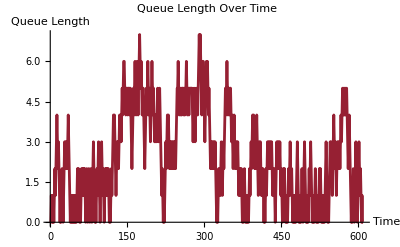

```mathematica
ListLinePlot[nlist1+nlist2,AxesLabel->{"Time","Queue Length"},PlotLabel->"Queue Length Over Time",PlotRange->All,PlotStyle->RGBColor[150/255,32/255,51/255]]
```

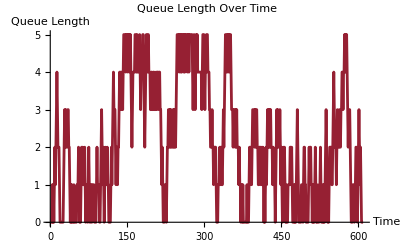

```mathematica
ListLinePlot[nlist1,AxesLabel->{"Time","Queue Length"},PlotLabel->"Queue Length Over Time",PlotRange->All,PlotStyle->RGBColor[150/255,32/255,51/255]]
```

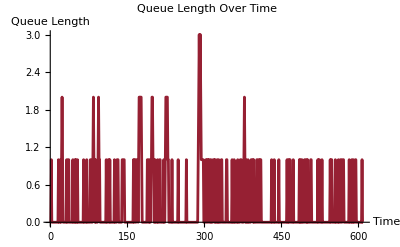

```mathematica
ListLinePlot[nlist2,AxesLabel->{"Time","Queue Length"},PlotLabel->"Queue Length Over Time",PlotRange->All,PlotStyle->RGBColor[150/255,32/255,51/255]]
```